Try to create the changing signal :

```mathematica
chirp[t_]:= Sin[2*t^2]
```

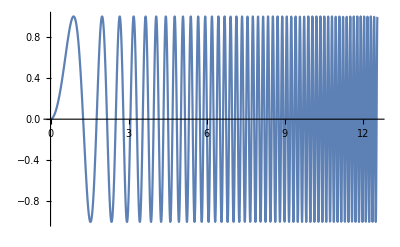

```mathematica
Plot[chirp[t],{t,0,4π}]
```

```mathematica
cwd = ContinuousWaveletTransform[Table[chirp[t],{t,0,4π}]]
```

ContinuousWaveletData[…]

```mathematica
WaveletScalogram[cwd]
```

-Graphics-